```mathematica
Task1[δδ_, ΔΔ_, ℵℵ_, kk_:1]:=Module[{δ=δδ, Δ=ΔΔ, ℵ=ℵℵ, k=kk},
success =False;
While[!success,
newOX = RandomReal[{δ, Δ}, 3]; (* Новое направление OX *)
newOX=newOX/Norm[newOX]; (* делаем его длины k *)
newOY = RandomReal[{δ, Δ}, 3]; (* С вероятностью 0 newOY==newOX *)
newOY=newOY/Norm[newOY];
success=success||(newOX.newOY > 1/3)
];
{newOX, newOY} = Orthogonalize[{newOX,newOY}];
newOZ = newOX×newOY;
{newOX, newOY, newOZ} *= k;
transitionMatrix = {newOX, newOY, newOZ};

Bsin[x_]:={0, Sin[k*x[[1]]],  Cos[k*x[[1]]]} ;
Bcos[x_]:={0, Cos[k*x[[1]]],  -Sin[k*x[[1]]]} ;
ϕ = RandomReal[{0, 2π}];
Bsincos[x_]:=Cos[ϕ]*Bcos[x]+Sin[ϕ]*Bsin[x];
B[x_]:=k^ℵ Bsincos[x];
Bx[x_]:=B[x][[1]]; (*сделать проекцию на новую систему*)
By[x_]:=B[x][[2]];
Bz[x_]:=B[x][[3]];
χ[r_]:=By[transitionMatrix.{0,0,0}] * Bz[r* transitionMatrix.{1, 0, 0}];
r= RandomReal[{0,1}];
{r,χ[r]}
];
```

```mathematica
transitionMatrix.{0,0,0}
```

{0.,0.,0.}

```mathematica
B=Cos[Φ]*Subscript[B, cos][О]+Sin[Φ]*Subscript[B, sin][О]
```

```mathematica
Subscript[B, cos][О]=(О, Cos[k*О],  -Sin[k*О]) = (0,1,0)
```

```mathematica
Subscript[B, sin][О]=(0, Sin[k*О],  Cos[k*О]) = (0,0,1)
```

```mathematica
B=  (0,Cos[Φ],Sin[Φ])
```

```mathematica
Subscript[B, z]=Sin[Φ]
```

```mathematica
{0,,  Cos[ϕ]*(-Sin[k*x[[1]]])} +{0,Sin[ϕ]* Sin[k*x[[1]]], Sin[ϕ]* Cos[k*x[[1]]]} ;
```

```mathematica
(Cos[ϕ]* Cos[k*x[[1]]] + Sin[ϕ]* Sin[k*x[[1]]]) * ( Cos[ϕ]*(-Sin[k*x[[1]]]) + Sin[ϕ]* Cos[k*x[[1]]])
```

```mathematica
k=1;
```

```mathematica
By[ϕ_]:=Cos[k * ϕ];
Bz[ϕ_,r_]:=Sin[k*ϕ+r];
```

```mathematica
χ[ϕ_, r_]:= (By[ϕ]) * (Bz[ϕ, r]);
```

```mathematica
data =Table[{rr = RandomReal[{0,1}],Mean[Table[χ[RandomReal[{0, 2π}]]/.{r->rr }, {i,1,1000}]]}, {i, 1, 1000}];
```

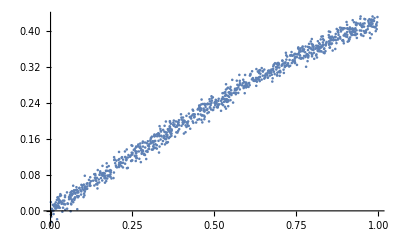

```mathematica
ListPlot[data]
```

```mathematica
Mean[Table[χ[RandomReal[{0, 2π}]]/.{r->0.2 }, {i,1, 1000}]]
```

0.107399

```mathematica
(π-π Cos[T])/(k T)/.{T->0.2} //N
```

0.313113

```mathematica
Table[{TT=RandomReal[{0,1}],(π-π Cos[T])/(k T)/.{T->RandomReal[{0,1}]}}, {i,1,1000}];
```

```mathematica
(∫_0^T (π Sin[r])/k ⅆr)/T
```

(π-π Cos[T])/(k T)

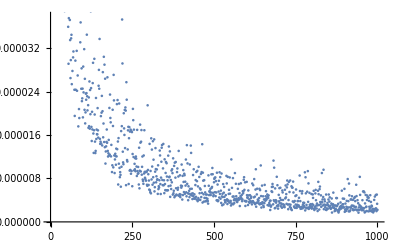

```mathematica
S=10000;
Table[Mean[Table[(π-π Cos[T])/(k T)/.{T->RandomReal[{1,S}]}, {i,1,1000}] ],{k,1, 1000}] // ListPlot
```

```mathematica
EvaluateMean[χχ_, rr_, nn_:10]:=Module[{χ=χχ,r=rr,n=nn},
Table[χ[r], {i, 0, n}] // Mean
];
```

```mathematica
δ = 1/1000; Δ = 1000; ℵ=1/2;
```

```mathematica
data =Table[Task1[δ, Δ, ℵ], {i, 1, 10000} ];
```

```mathematica
Table[Mean[Table[Task1[δ, Δ, ℵ][[2]], {i, 1, 10000} ]],{j,1,10}]
```

{-0.126904,-0.129888,-0.121972,-0.125203,-0.11877,-0.124718,-0.120823,-0.129896,-0.124735,-0.121642}

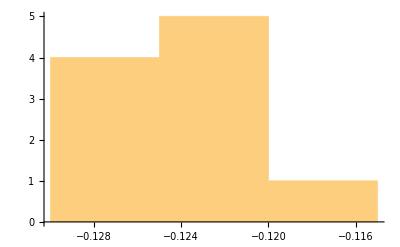

```mathematica
Histogram[%]
```

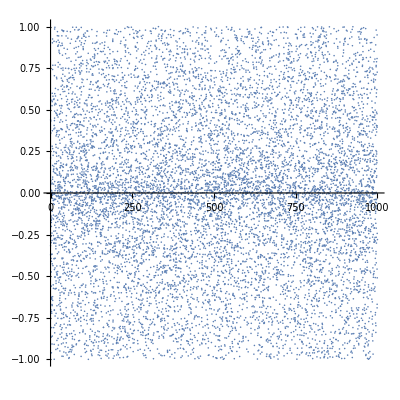

```mathematica
ListPlot[data, AspectRatio->1]
```

```mathematica
Table[Total[Take[data, {i*10000/2+1, (i+1)*10000/2}]],{i,0, 1}]
```

{{2.50959×10^6,5.99034},{2.52984×10^6,-94.8537}}

```mathematica
Total[data]
```

{5.03942×10^6,-88.8634}

```mathematica
Table[Task1[δ, Δ, ℵ][0], {i,0,20}]
```

{0.996274,0.240368,0.648282,-0.285782,0.558372,-0.49262,-0.33011,-0.524391,-0.485986,-0.423272,-0.987324,0.57056,0.96121,0.679408,-0.301471,-0.586807,0.934115,-0.982104,-0.605979,0.0121699,0.781084}

```mathematica
δ = 1/1000; Δ = 1000; ℵ=1/10;n=1000;
```

```mathematica
data = Table[EvaluateMean[Task1[δ, Δ, ℵ], r], {r, 1, 10000, 1}]
```

{-0.789226,-0.429287,-0.454091,0.298976,-0.333848,0.342168,9989,0.927527,-0.969499,0.0729298,0.430797,-0.216301}
 |  |  |  |

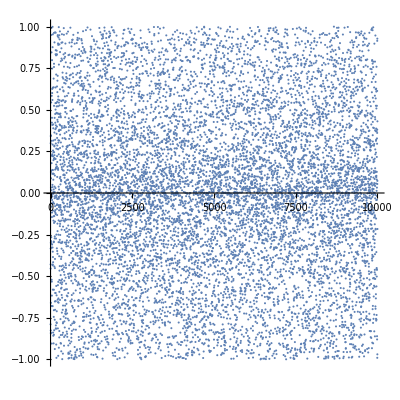

```mathematica
ListPlot[data, AspectRatio->1]
```

```mathematica
δ = 1/1000; Δ = 1000; ℵ=1.5;n=1000;
```

```mathematica
data = Table[EvaluateMean[Task1[δ, Δ, ℵ], r], {r, 1000, 10000, 1}]
```

{-0.456951,-0.00724531,0.534017,-0.18149,0.476045,0.470613,8990,0.685833,-0.871837,0.535014,-0.11491,-0.640105}
 |  |  |  |

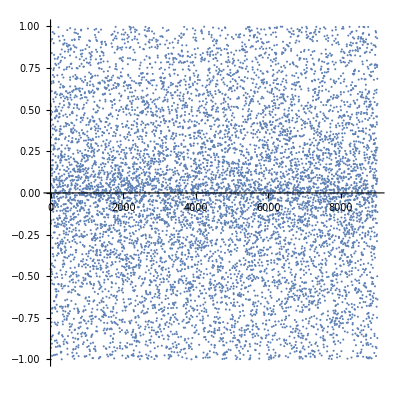

```mathematica
ListPlot[data, AspectRatio->1]
```

```mathematica
!True
```

False